```mathematica
<<peeters`;
peeters`setGitDir["../project/figures/phy452-basicstatmech"]
fs=Style[#,FontSize->14]&;
```

/Users/pjoot/project/figures/phy452-basicstatmech

## Problem 1

### Check my hand calculations for 2, 3, 4, 5 dimensional spheres.

```mathematica
(* wikipedia formula *)
Clear[nSphereVolume, nSphereArea]
nSphereVolume[n_] = r^n Pi^(n/2)/Gamma[n/2 + 1] ;
Table[nSphereVolume[i] ,{i,0,7}]
nSphereArea[n_] = n r^(n-1) Pi^(n/2)/Gamma[n/2 + 1] ;
Table[nSphereArea[i] ,{i,1,7}]
```

{1,2 r,π r^2,(4 π r^3)/3,(π^2 r^4)/2,(8 π^2 r^5)/15,(π^3 r^6)/6,(16 π^3 r^7)/105}

{2,2 π r,4 π r^2,2 π^2 r^3,(8 π^2 r^4)/3,π^3 r^5,(16 π^3 r^6)/15}

```mathematica
(* to evaluate the recurrence relation I calculated, need a product of sine power integrals, which simplifies nicely *)
Clear[i]
i[n_] = Integrate[ Sin[t]^(n), {t,0,Pi/2}, Assumptions->Element[n,Integers]&& n>=0 ]
i[2] i[1]
FullSimplify[i[n-2]i[n-3], Element[n,Integers]&& n> 0]
```

(√π Gamma[(1+n)/2])/(2 Gamma[1+n/2])

π/4

π/(2 (-2+n))

## Problem 3. state counting spins.

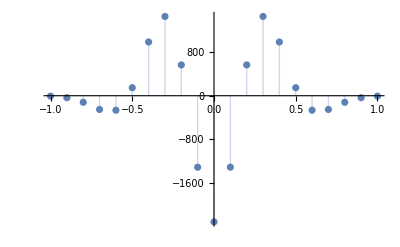

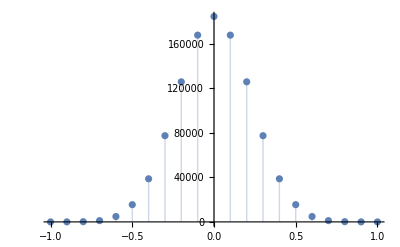

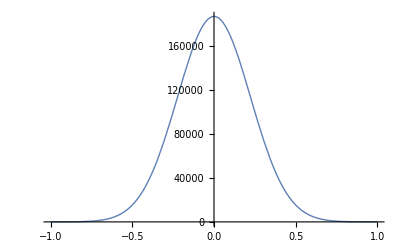

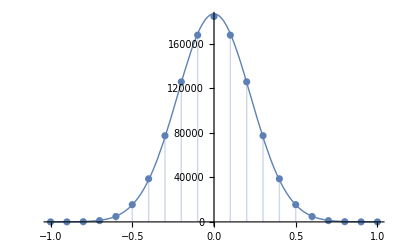

{statMechProblemSet3Problem3Fig1.eps,statMechProblemSet3Problem3Fig1pn.png}

{statMechProblemSet3Problem3Fig2.eps,statMechProblemSet3Problem3Fig2pn.png}

```mathematica
Clear[g, gEst, distG, gDiff]
g[n_, m_] = n!/(n/2(1 - m))!/(n/2(1+m))! ;
gEst[n_, m_] =  2^n E^(-m^2 n/2) Sqrt[ 2/(Pi n)] ;
distG[n_] := Table[{m, g[n, m]},{m,-1,1, 2/n}] ;
gDiff[n_] := Table[{m, g[n, m] - gEst[n, m]},{m,-1,1, 2/n}] ;
(*Module[{n=20},ListLinePlot[ distG[20] , Filling->Axis]]*)
Clear[statMechProblemSet3Problem3Fig2, p2]
Module[{n=20},
ListPlot[  gDiff[n], 
PlotStyle->Thick,
Filling->Axis]]
statMechProblemSet3Problem3Fig2 = Module[{n=20},
ListPlot[ distG[n] , 
PlotStyle->Thick,
Filling->Axis]]
p2 = Module[{n=20},
Plot[ gEst[n, m], {m,-1,1} ,
PlotStyle->Thick
] ]
statMechProblemSet3Problem3Fig1 = Show[{p1, p2}]
peeters`exportForLatex["statMechProblemSet3Problem3Fig1",statMechProblemSet3Problem3Fig1]
peeters`exportForLatex["statMechProblemSet3Problem3Fig2",statMechProblemSet3Problem3Fig2]

(*Integrate[gEst[20, m],{m, -Infinity, Infinity}]*)
```

## Problem 2.

```mathematica
Integrate[Sqrt[1 + a Cos[x]],{x,0,2 Pi}]
HoldForm[Integrate[Sqrt[1 + a Cos[x]],x]] // TraditionalForm
Integrate[Sqrt[1 + a Cos[x]],x] // TraditionalForm
```

ConditionalExpression[2 (√(1-a) EllipticE[(2 a)/(-1+a)]+√(1+a) EllipticE[(2 a)/(1+a)]),(Re[1/a]≥1||1+Re[1/a]≤0||1/a∉Reals)&&Re[a]<1&&1+Re[a]>0]

∫√(1+a cos(x))ⅆx

(2 √(a cos(x)+1) x/2(2 a)/(a+1))/(√((a cos(x)+1)/(a+1)))

```mathematica
Clear[eta]
eta = Pi/Sqrt[18]

2 Quantity[5,"Angstroms"] (300)^(1/3) // N

2 Quantity[5,"Angstroms"] (300/eta)^(1/3) // N

Quantity[10,"Angstroms"] Sqrt[300] // N
(*Quantity[10,"Angstroms"] (Sqrt[300-1]+1) // N
Sqrt[300] // N
Sqrt[300-1] + 1 // N*)
```

π/(3 √2)

66.9433

73.995

173.205

10 √3 1 nm  (nanometer)

### Face centered cubic

```mathematica
LatticeData["FaceCenteredCubic","Image"]  // InputForm
LatticeData["FaceCenteredCubic","PackingRadius"] 
spaceFilledPlot[latticeType_]:=LatticeData[latticeType,"Image"]/.Sphere[pt_,r_]:>{Opacity[1],Sphere[pt,LatticeData[latticeType,"PackingRadius"]]}

s = spaceFilledPlot["FaceCenteredCubic"]
Show[s,PlotRange->{{-1,1},{-1,1},{-1,1}}]
```

1/(√2)

-Graphics3D-

-Graphics3D-

```mathematica
Graphics3D[{GraphicsComplex[{{-1, -1, -1}, {-1, -1, 1}, {-1, 1, -1}, 
    {-1, 1, 1}, {1, -1, -1}, {1, -1, 1}, {1, 1, -1}, {1, 1, 1}, 
    {0, 0, 1}, {1, 0, 0}, {0, 1, 0}, {-1, 0, 0}, {0, 0, -1}, 
    {0, -1, 0}}, {{EdgeForm[GrayLevel[0.8]], Opacity[0.1], 
     Polygon[{{8, 4, 2, 6}, {8, 6, 5, 7}, {8, 7, 3, 4}, {4, 3, 1, 2}, 
       {1, 3, 7, 5}, {2, 1, 5, 6}}]}, {GrayLevel[0.8], 
     Line[{{9, 8}, {9, 4}, {9, 2}, {9, 6}, {10, 8}, {10, 6}, {10, 5}, 
       {10, 7}, {11, 8}, {11, 7}, {11, 3}, {11, 4}, {12, 4}, {12, 3}, 
       {12, 1}, {12, 2}, {13, 1}, {13, 3}, {13, 7}, {13, 5}, {14, 2}, 
       {14, 1}, {14, 5}, {14, 6}}]}}], 
  {GrayLevel[0], Specularity[GrayLevel[1], 5], 
   {Sphere[{-1, -1, -1}, 0.06], Sphere[{-1, -1, 1}, 0.06], 
    Sphere[{-1, 1, -1}, 0.06], Sphere[{-1, 1, 1}, 0.06], 
    Sphere[{1, -1, -1}, 0.06], Sphere[{1, -1, 1}, 0.06], 
    Sphere[{1, 1, -1}, 0.06], Sphere[{1, 1, 1}, 0.06], 
    Sphere[{0, 0, 1}, 0.06], Sphere[{1, 0, 0}, 0.06], 
    Sphere[{0, 1, 0}, 0.06], Sphere[{-1, 0, 0}, 0.06], 
    Sphere[{0, 0, -1}, 0.06], Sphere[{0, -1, 0}, 0.06]}}}, 
 Boxed -> False, ViewPoint -> {4, 5/3, 1}]
 
 LatticeData[]
```

-Graphics3D-

{BaseCenteredMonoclinic,BaseCenteredOrthorhombic,BodyCenteredCubic,BodyCenteredOrthorhombic,CenteredTetragonal,CoxeterTodd,FaceCenteredCubic,FaceCenteredOrthorhombic,HexagonalClosePacking,HexagonalLattice,KorkineZolotarev,Leech,SimpleCubic,SimpleHexagonal,SimpleMonoclinic,SimpleOrthorhombic,SimpleTetragonal,SimpleTriclinic,SimpleTrigonal,SquareLattice,TetrahedralPacking}

```mathematica
volumetricPlot[latticeType_]:=Module[
{img=LatticeData[latticeType,"Image"],r=LatticeData[latticeType,"PackingRadius"]},
Show[
img/.Sphere[pt_,r_]:>{},Map[RegionPlot3D[(EuclideanDistance[{x,y,z},#]<r),{x,-1,1},{y,-1,1},{z,-1,1},Mesh->False,PlotStyle->Opacity[.9]]&,Cases[img,Sphere[pos_,_]:>pos,Infinity]]
]
]

volumetricPlot["FaceCenteredCubic"]
volumetricPlot["HexagonalClosePacking"] (* buggy lattice data: can-a-latticedata-image-be-displayed-in-a-space-filled-fashion *)
volumetricPlot["BodyCenteredCubic"]
volumetricPlot["SimpleCubic"] (* also looks buggy *)
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

```mathematica
Block[{r, i},
r = 1 ;

i = Graphics3D[ 
 {Opacity[0.5],
Cuboid[{-1,-1,-1}, {1,1,1}],
Opacity[.9],
(*Cylinder[{{1, 1, 1}, {1, 1, 1}}, 1] ,*)
Sphere[{-1, -1, -1}, r], 
Sphere[{-1, -1, 1}, r], 
Sphere[{-1, 1, -1}, r], 
Sphere[{-1, 1, 1}, r],
Sphere[{1, -1, -1}, r], 
Sphere[{1, -1, 1}, r], 
Sphere[{1, 1, -1}, r], 
Sphere[{1, 1, 1}, r] }, 
Boxed -> False, ViewPoint -> {4, 5/3, 1}
] ;
Show[i, PlotRange -> {{-1, 1}, {-1,1}, {-1,1}}]
]
```

-Graphics3D-